Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→0.49455-0.134864 x}}

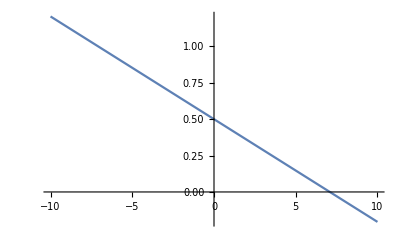

```mathematica
sig0 = {{0.27681, 0.0112287}, {0.0112287, 0.0361191}};
sig1 = {{0.159748, -0.015575}, {-0.015575, 0.0299584}};
m0 = {{-0.22147}, {0.325755}};
m1 = {{0.0759543},{0.682969}};
bigSig = 1/2( sig0 + sig1);
prior0 = 1/2;
prior1 = 1/2;
X = {{x}, {y}};
post0 = 1/ (2 * Pi *Det[bigSig]^(1/2)) * Exp[-0.5 *Transpose[ X - m0].Inverse[bigSig].(X-m0)];post1 = 1/ (2*Pi*Det[bigSig]^(1/2)) * Exp[-0.5 *Transpose[ X - m1].Inverse[bigSig].(X-m1)];
Solve[post0 == post1,y]//Simplify
Plot[0.49923559602493417-0.07045843129044978 x, {x, -10, 10}]
```